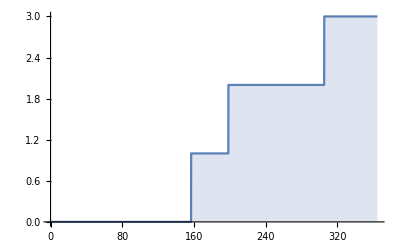

```mathematica
Clear["Global`*"]
(* Generating wealth by power plant operation subject to stochastic processes *)
(* electricty prices move according to an Ornstein-Uhlenbeck Process *)
(* Power plant sometimes is unavailable due to technical failure, described by a Poisson process *)

data=RandomFunction[PoissonProcess[0.004],{0,365,.1}];
ListLinePlot[data,Filling->Axis]
```

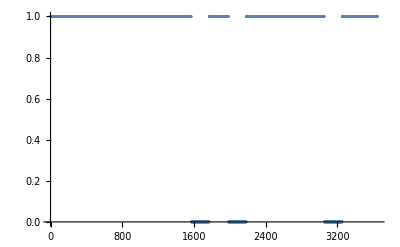

```mathematica
GPI[x_]:=Module[{nn=0,uptime={},events,Nout=200,k},
events=x["Values"];
nn=Length[events];

For[j=1,j<nn,j++,If[(events[[j+1]]-events[[j+0]])>0,For[k=0,k<Nout,k++,AppendTo[uptime,0]];j=j+Nout,AppendTo[uptime,1]]];
uptime
];
ListPlot[GPI[data]]
```

```mathematica
Nz=Length[data["Values"]];
Gamma03[x_,gpi_]:=Module[{nn=0,j=0,sum=0,prices},
prices=x["Values"];
nn=Length[prices];
For[j=1,j<nn-10,j++,sum=sum+gpi[[j]]*prices[[j]]];
sum
];

Gamma03[RandomFunction[OrnsteinUhlenbeckProcess[40,12,.3],{0,365,.1}],GPI[data]]
```

123283.

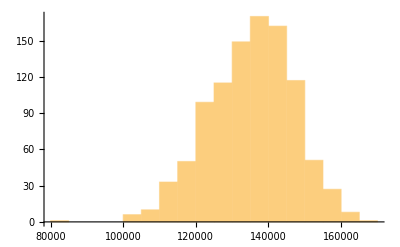

```mathematica
Wealth={};
Nz=1000;
For[w=1,w<Nz,w++,AppendTo[Wealth,Gamma03[RandomFunction[OrnsteinUhlenbeckProcess[40,12,.3],{0,365,.1}],GPI[RandomFunction[PoissonProcess[0.004],{0,365,.1}]]]]];
Histogram[Wealth]
```